# P2: Orthogonality

The gold-standard most stable linear algebra computations are based on operations with orthogonal matrices.  We need to be able to build rotations (and associated projectors) to do useful tasks.

## Projectors and Orthogonality

### Calculus II

In Calculus II you defined projectors onto a vector u as an operator (clearly linear although you may not have bothered saying it) as 
	v→(<v,u>)/(<u,u>)u=(v.u)/(u.u)u
You immediately realized that this was cleaner if u was normalized! The simpler formula for the projector onto a unit (||u||=1) vector 
	v→(v.u)u
and the complementary projection onto u^⊥
	v→v-(v.u)u
hopefully look familiar! Since these are linear operators they have matrices!

We want to know how to tell if a matrix is a projection.

We want to know how to efficiently build useful projection matrices.

### Linear Algebra: Eigenstuff

In linear algebra you learned eigenvalue-eigenvector pairs of A satisfy
	A.v=λ v.
You did not learn how to compute them for large matrices!

You did learn that for real symmetric m×m matrices A=Aᵀ:

The m eigenvalues λ_k were real.

The m eigenvectors v_k could be chosen real and orthogonal!

### Projector: Definitions etc.

An m×m matrix P is a projector if P^2=P.P=P.  The fancy word for this property is “Idempotent”. It simply says multiplying by P once is the same as doing it more than once!

For a projector P the complementary projector is I-P

An orthogonal projector has P=P^*

Eigenvalues of P are all either 1 or 0.

### Householder Reflector

The Householder Reflector associated with an orthogonal projector P is the Orthogonal matrix Q=I-2P.

### Tall Skinny A: Orthogonal Projector onto Column Space of A

If A is full rank then the orthogonal projector onto the column space of A is P=A.(A^*.A)^-1.A^*

### Tall Skinny Q: Orthogonal Projector onto Orthogonal basis

If a Tall-Skinny m×n matrix Q has orthogonal columns then Q^*.Q=I_n! and the orthogonal projector is P=Q.Q^*.

This has limited utility until we know how compute an orthogonal Q

### Computations

Checking some stuff.

```mathematica
{m,n}={17,4};
A=RandomReal[{-1,1},{m,n}];
P=A.Inverse[Aᵀ.A].Aᵀ;
H=IdentityMatrix[m]-2P;
{Dimensions[P],Map[Norm,{P-P.P,P-Pᵀ,H.Hᵀ-IdentityMatrix[m]}]}
MatrixPlot[P];
```

{{17,17},{5.26644×10^-16,1.54276×10^-16,1.87372×10^-15}}

```mathematica
{m,n}={17,4};
A=RandomReal[{-1,1},{m,n}];
P=A.Inverse[Aᵀ.A].Aᵀ; H=IdentityMatrix[m]-2P;
Map[Eigenvalues,{P,H}]
```

{{1.,1.,1.,1.,3.38763×10^-16,2.31839×10^-16,-1.65756×10^-16,1.38996×10^-16,1.10855×10^-16,-7.51878×10^-17,5.48409×10^-17,-4.88653×10^-17,2.97816×10^-17,-1.76579×10^-17,-4.74608×10^-18,2.26945×10^-18,1.12772×10^-18},{1.,-1.,1.,-1.,1.,1.,1.,1.,-1.,1.,1.,1.,1.,1.,1.,-1.,1.}}

## QR Decomposition

### Matrices with orthogonal columns are useful!

Our target is to construct an orthogonal basis for the column space of a Tall-Skinny m×n matrix
	A=[a_1|a_2|…|a_n].
This basis is naturally represented by a Tall-Skinny m×n matrix
	Q=[q_1|q_2|…|q_n].
We will learn how to compute a QR decomposition A=Q.R where the new matrix R (which tells us how to combine the columns of A to compute Q) is upper triangular!

Every software package has a QR decomposition.  Different packages return the bits in different ways! Always read the documentation and check! Mathematica returns Q on its side!

{1.91925×10^-15,4.50855×10^-16}

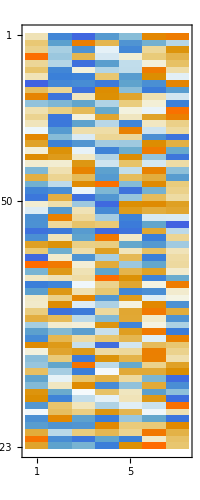
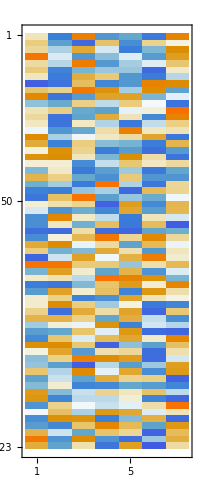
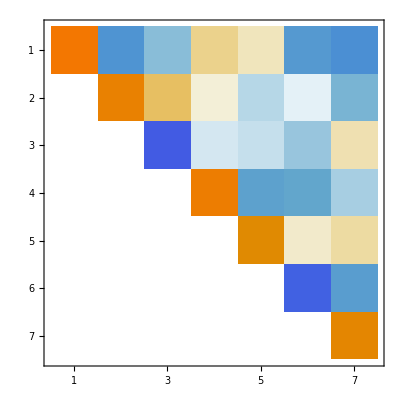

```mathematica
{m,n}={123,7};
A=RandomReal[{-1,1},{m,n}]; 
{Q,R}=QRDecomposition[A];
(* Mathematica #$#@$ returns Q on it side *)
Q=Qᵀ;
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
Map[MatrixPlot,{A,Q,R}]
```

We are going to learn one way the computer could do this.  Well actually we are going to learn a bunch but the first one is called the Gram-Schmidt process.

### Gram-Schmidt: Idea

The motto here is start at the very beginning of
	A=[a_1|a_2|…|a_n]
and work through the columns!

First, normalize the first column by dividing by ||a_1|| and define
	q_1=a_1/(||a_1||).

Next, project out the component of a_2 in the direction of q_1
	q_2=a_2-(a_2.q_1)q_1
and normalize
	q_2=q_2/||q_2||.
Note we have recycled q_2 repeatedly to accumulate the correct expression.

The next step is more of the same but we need to get a bit more organized!  Pick the next column
	w=a_3
project out the components in q_1 and q_2
	w | = | w-(w.q_1)q_1
w | = | w-(w.q_2)q_2
and normalize
	q_3=w/||w||.
I am using w as mnemonic for work vector!

The next step is more of the same but we need to get a bit more organized!  Pick the next column
	w=a_4
project out the components in q_1 and q_2
	w | = | w-(w.q_1)q_1
w | = | w-(w.q_2)q_2
w | = | w-(w.q_3)q_3
and normalize
	q_4=w/||w||.

All we have to do is keep going until we run out of columns!  We are left with the tall-skinny matrix Q.  The only problem is we do not have the recipe for how we combined the columns: it is all stored in the inner products and scalings of the vectors.

### Gram-Schmidt: Manual

Here is a hand walk through of for a three column matrix! I am saving the coefficients so that we can see where they go!

```mathematica
{m,n}={5,3};
A=RandomReal[{-1,1},{m,n}];
(* First column *)
 v=A⟦All,1⟧;
c1=Norm[v];
q1 =v/c1;
(* second column *)
v=A⟦All,2⟧;
c21 =v.q1;
v=v-c21 q1;
c2=Norm[v];
q2 =v/c2;
(* Third column *)
v=A⟦All,3⟧;
c31 =v.q1;
v=v-c31 q1;
c32 =v.q2;
v=v-c32 q2;
c3=Norm[v];
q3 =v/c3;
MyQ={q1,q2,q3};
{c1,{c21,c2},{c31,c32,c3}}
```

{0.861131,{0.922836,0.88536},{-0.548136,-0.0360935,1.18991}}

Lets compare to the built-in QR

```mathematica
{BuiltInQ,BuiltInR}=QRDecomposition[A];
BuiltInR
```

{{-0.861131,-0.922836,0.548136},{0.,0.88536,-0.0360935},{0.,0.,1.18991}}

Our numbers match (except for the signs) and I think we can work out how to construct R

### Gram-Schmidt: Script

Here is a preliminary script!

{4.48992×10^-16,1.19083×10^-15}

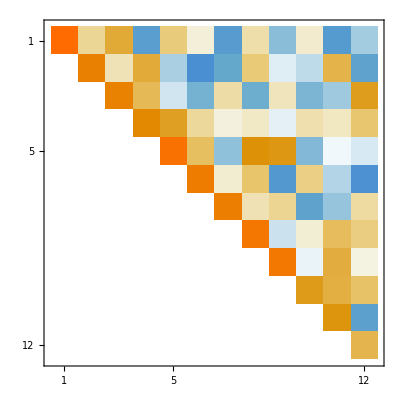

```mathematica
{m,n}={14,12};
A=RandomReal[{-1,1},{m,n}];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}]
(* Check that we computed a QR Decomposition *)
Map[Norm,{A-Q.R,Transpose[Q].Q-IdentityMatrix[n]}]
(*{OrthogonalMatrixQ[Q],UpperTriangularMatrixQ[R]}*)
MatrixPlot[R]
```

### Gram-Schmidt: Function

Here is a function to hide all the crud!

```mathematica
MyGramSchmidt[A_]:= Module[{m,n,Q,R,v},
{m,n}=Dimensions[A];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧,
{j,1,n}];
{Q,R}]
```

Here is a test

```mathematica
{m,n}={700,450};
A=RandomReal[{-1,1},{m,n}];
AbsoluteTiming[{Q,R}=MyGramSchmidt[A];]
AbsoluteTiming[{Q2,R2}=QRDecomposition[A];]
AbsoluteTiming[Z=Q2ᵀ;]
(* Check that we computed a QR Decomposition *)
Map[Norm,{A-Q.R,Qᵀ.Q-IdentityMatrix[n]}]
UpperTriangularMatrixQ[R]
```

{1.98198,Null}

{0.0155857,Null}

{0.0009007,Null}

{1.98574×10^-14,2.11361×10^-15}

True

### Efficiency: Math Libraries

The built in QR decomposition is going to be MUCH faster than any code we write. The reason is that the basic QR computation is the foundation for a lot of other fancier computations.  As a result, a substantial effort has been made to make it as efficient as possible.  This includes economizing storage and computation and communication.

All the higher level tools rely on libraries of math functions.  The lowest level is called BLAS for Basic Linear Algebra Subprograms which are designed to squeeze every possible bit of performance out of all sorts of hardware.

One of the reasons Julia is fast (the Julia folks use the word performant) and one of the reasons we are going to look at Julia is that it makes it easy to access these libraries. Good code uses these libraries!

```mathematica
{m,n}={1500,111};
A=RandomReal[{-1,1},{m,n}];
Timing[{Q,R}=MyGramSchmidt[A];]
Timing[{Q,R}=QRDecomposition[A];]
```

{0.515625,Null}

{0.015625,Null}

### Math Libraries

Math libraries (BLAS, MKL, ...) are portable, fast, and an all round good idea!

We are about to see that subtle algorithmic differences can significantly impact stability and performance!

Real QR codes would never do GS (7.1) when MGS (8.1) is better and almost the same amount of work. Both treat R as the main product and Q as a byproduct.

Most of the time Q is the thing folks want and R is just thrown away. In this case the Householder algorithm we are going to talk about later which targets Q gives more orthogonal matrices.

### Modified Gram-Schmidt

Here is our implementation of GS 7.1

```mathematica
MyGramSchmidt[A_]:= Module[{m,n,Q,R,v},
{m,n}=Dimensions[A];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=Q⟦All,i⟧.A⟦All,j⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}];
{Q,R}]
```

Here is an implementation of Modified GS 8.1

```mathematica
MyModifiedGramSchmidt[A_]:= Module[{m,n,Q,R,V},
{m,n}=Dimensions[A];
V=A;Q=0*A; R=ConstantArray[0,{n,n}];
Do[
R⟦i,i⟧=Norm[V⟦All,i⟧];
Q⟦All,i⟧=V⟦All,i⟧/R⟦i,i⟧;
Do[
R⟦i,j⟧=Q⟦All,i⟧.V⟦All,j⟧;
V⟦All,j⟧=V⟦All,j⟧-R⟦i,j⟧ Q⟦All,i⟧,
{j,i+1,n}],
{i,1,n}];
{Q,R}]
```

Testing and comparing the two versions! Both work.

```mathematica
{m,n}={400,399};
A=RandomReal[{-1,1},{m,n}];
TableForm[
Table[
time=AbsoluteTiming[{Q,R}=qr[A];]⟦1⟧;{qr,time,Norm[Qᵀ.Q-IdentityMatrix[n]],Norm[A-Q.R]},
{ qr,{MyGramSchmidt,MyModifiedGramSchmidt}}],
TableHeadings->{None,{"Algorithm","Sec","Orth Res","Residual"}}
]
```

Algorithm | Sec | Orth Res | Residual
MyGramSchmidt | 2.00313 | 5.88963×10^-13 | 1.5203×10^-14
MyModifiedGramSchmidt | 2.94135 | 6.64399×10^-14 | 1.52477×10^-14

Just for comparison!

```mathematica
time=AbsoluteTiming[{Q,R}=QRDecomposition[A];]⟦1⟧;
Q=Qᵀ; 
{time,Norm[Qᵀ.Q-IdentityMatrix[n]],Norm[A-Q.R]}
```

{0.018914,4.55157×10^-15,5.1046×10^-14}

### Modified vs Classical Gram-Schmidt vs QR implementation

One of them is better! Neither is the best! The issues are subtle but real!  There are two main problems: small entries in R can be computed inaccurately and the Q could lose orthogonality due to only 16 digits of computer arithmetic!  MKS is better at resolving R accurately (we will pay more attention to this later) but both struggle to generate fully accurate orthogonal matrices  when the going gets tough

Random matrices are unlikely to highlight these problems.  We need to make tricksy matrices.

#### Nearly Parallel Columns

Both of our Gram-Schmidt algorithms struggle with nearly parallel columns.   The important thing is that better algorithms are used in built-in QR calls.

```mathematica
m=32;
ϵ =0.0000001;
{u,v}= RandomReal[{-1,1},{2,m}];
A=KroneckerProduct[u,v]+ϵ RandomReal[{-1,1},{m,m}];
MatrixPlot[A];
{Q,R}=QRDecomposition[A];Q=Qᵀ;
{Qgs,Rgs}=MyGramSchmidt[A];
{Qmgs,Rmgs}=MyModifiedGramSchmidt[A];
TableForm[
Map[{Norm[#⟦1⟧.#⟦1⟧ᵀ-IdentityMatrix[m]],Norm[A-#⟦1⟧.#⟦2⟧]}&,
{{Q,R},{Qgs,Rgs},{Qmgs,Rmgs}}],
TableHeadings->{{"QR","GS","MGS"},{"||Q.Qᵀ-I||","||A-Q.R||"}}]
```

| ||Q.Qᵀ-I|| | ||A-Q.R||
QR | 1.05032×10^-15 | 3.29869×10^-15
GS | 1.68308 | 1.13076×10^-15
MGS | 1.16029×10^-7 | 9.86348×10^-16

This better algorithm designs and accumulates a sequence of orthogonal matrices Q_1,Q_2,… at each stage!  The simplest version of this is a “Householder” reflector.

### Householder Reflector

We have already seen that H=I-2P is a symmetric orthogonal matrix if P is an orthogonal projection.   Since it is straight-forward lets do it again.  Assume P=Pᵀ and P.P=P then
	Hᵀ.H=(I-2P)ᵀ.(I-2P)=(I-2P).(I-2P)=I-2P-2P+4P.P=I-4P+4p=I.
A Householder reflection chooses the first projection P_1 so that H_1=I-2 P_1satisfies H_1.a_1=±||a_1||e_1. You then repeat  the process (with some bookkeeping) until you run out of columns!

Given a we need to choose P to make 
	(I-2 P).a=±||a||e_1
or equivalently
	-2 P.a=-a±||a||e_1
or equivalently
	2 P.a=a∓||a||e_1
If v is a unit vector the projection P=I-v⊗v has m-1 Degrees Of Freedom (DOF). It is possible to choose v to do what we want!  We want v to satisfy
	2 (I-v⊗v).a=a∓||a||e_1
or equivalently
	2 a-2v (v.a)=a∓||a||e_1
or equivalently
	-2v (v.a)=-a∓||a||e_1 ⟹ v(v.a)=(1/2)(a±||a||e_1)
In words, v is a unit vector parallel to a±||a||e_1.

It is easy to check that this works.

```mathematica
m=12;
a=RandomReal[{-1,1},m];
v=a; 
v⟦1⟧=v⟦1⟧-Norm[a];
v=Normalize[v];
P=IdentityMatrix[m]-KroneckerProduct[v,v];
H=IdentityMatrix[m]- 2 P;
Norm[H.Hᵀ -IdentityMatrix[m]]
Chop[H.a]
```

4.98357×10^-16

{-2.22013,0,0,0,0,0,0,0,0,0,0,0}

## Householder QR (lecture 10)

### Householder Reflector Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=23;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

5.78063×10^-16

{2.88158,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflector Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=12467;
{x,a}=RandomReal[{-1,1},{2,m}];
AbsoluteTiming[
Q=HouseMat[a];
Q.x;
]
AbsoluteTiming[
HouseActionVec[x,a];
]
```

{2.3174,Null}

{0.00048,Null}

### Householder QR: Script Version 1

Here is a manual reduction of a Tall Skinny matrix A to upper triangular using Householder reflections. We are writing over the top of A to save space.  The fancy word for this is an “in-place” computation.

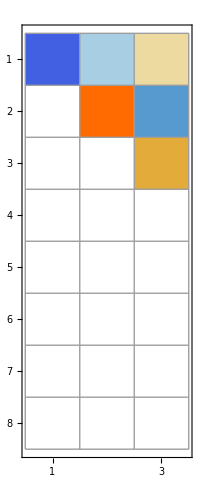
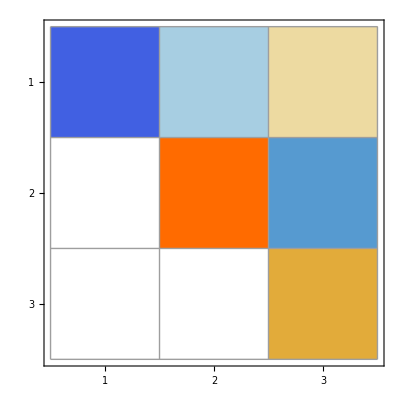

```mathematica
{m,n}={8,3};
A0=A=RandomReal[{-1,1},{m,n}];
{Q,R}=QRDecomposition[A];
a1=A⟦1;;-1,1⟧;
A⟦1;;-1,1⟧=HouseActionVec[A⟦1;;-1,1⟧,a1];
A⟦1;;-1,2⟧=HouseActionVec[A⟦1;;-1,2⟧,a1];
A⟦1;;-1,3⟧=HouseActionVec[A⟦1;;-1,3⟧,a1];
MatrixPlot[Chop[A],Mesh->All];
a2=A⟦2;;-1,2⟧;
A⟦2;;-1,2⟧=HouseActionVec[A⟦2;;-1,2⟧,a2];
A⟦2;;-1,3⟧=HouseActionVec[A⟦2;;-1,3⟧,a2];
MatrixPlot[Chop[A],Mesh->All];
a3=A⟦3;;-1,3⟧;
A⟦3;;-1,3⟧=HouseActionVec[A⟦3;;-1,3⟧,a3];
{MatrixPlot[Chop[A],Mesh->All],MatrixPlot[R,Mesh->All]}
```

We have worked out what the QR algorithm (at least for R) is!

```mathematica
R=QRDecomposition[A0]⟦2⟧;
Chop[{A⟦1;;n⟧,R}]
```

{{{-1.78851,-0.0685301,0.154593},{0,1.96665,-0.458363},{0,0,0.691489}},{{-1.78851,-0.0685301,0.154593},{0,1.96665,-0.458363},{0,0,0.691489}}}

Notes:

We should do the columns together.

We do not have Q because we did not save it!  It is not a good idea to compute it at the end as Q=A.R^-1

Performant library code saves the Householder vectors (on top of the newly created zeros) and only builds an explicit Q matrix if needed.

### Householder QR: Script Version 2

Here is a less-manual script reducing a Tall Skinny matrix A to upper triangular using Householder reflections again overwriting A.

12

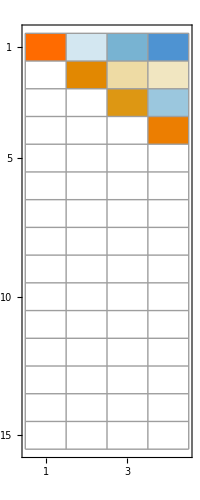

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}];
Do[
v=HouseVec[A⟦i;;-1,i⟧];
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n}]
{Q,R} =QRDecomposition[A];
TabView[Map[MatrixForm,Chop[{R,A⟦1;;n,1;;n⟧}]]]
MatrixPlot[Chop[A],Mesh->All]
```

We are going to save the Householder vectors (so that we can build Q) in the next version!

### Householder QR: Script Version 3

Here is a less-manual script reducing a Tall Skinny matrix A to upper triangular overwriting A and saving the Householder vectors.

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}]; V=0.0*A;
Do[
v=HouseVec[A⟦i;;-1,i⟧]; V⟦i;;-1,i⟧=v;
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n}]
{Q,R} =QRDecomposition[A];
TabView[Map[MatrixPlot[#, Mesh->All]&,{Chop[A],V}]]
```

12

Note: Performant code stuffs the reduced A and Householder vectors V together in a single rectangular matrix.

Yes they overlap! You either need a little extra storage vector (for the diagonals) or you need to remember that since the Householder vectors are unit vectors they have one less Degree of Freedom.

Next we are going to work out how to build the Householder Q from all the Householder vectors in V.

### Householder QR: Function

Here is a function reducing a Tall Skinny matrix A to upper triangular which overwrites A and returns the Householder vectors.

Here is an in-place Mathematica code.  HoldFirst prevents evaluation of the first argument A! As a result, the name (memory address) of the matrix A is handed to the function rather than making a copy of the matrix A and handing the copy off to the function!  The specified operations are done on the “original” matrix and we do not need to return anything! Since matrices can be (in the real world almost always are) very large this is much more efficient.

```mathematica
SetAttributes[MyQR,HoldFirst]
MyQR[A_]:= Module[{m,n,v,V},
{m,n}=Dimensions[A];
V=ConstantArray[0,{m,n}];
(* Householder Reduction from Script Version 3 *)
Do[
v=HouseVec[A⟦i;;-1,i⟧]; V⟦i;;-1,i⟧=v;
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}],
{i,1,n}];
(* Returns Householder vectors in V *)
V
]
```

As always TEST as best you can!  To test properly we need the Q!

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}]; V=0.0*A;
V=MyQR[A];
R=Chop[A⟦1;;n,1;;n⟧]
```

{{-2.51767,-0.532725,0.29488,0.079178},{0,-2.11629,0.144502,-0.54592},{0,0,-2.2619,0.843195},{0,0,0,-1.49213}}

Next we are going to work out how to build the Householder Q from all the Householder vectors in V.

### Householder Q

#### Building Q from V Plan 1

We reduce the tall-skinny m×n matrix A_0 with a sequence of Householder reflectors that created zeros in the lower triangle of A_0

The first reflector H_1=I-v_1⊗v_1is m×m.  After the first step we have A_1=H_1.A_0 with a reduced first column.

The second one I-v_2⊗v_2is (m-1)×(m-1) which acts only on the lower (m-1)×n portion of A_1to give A_2.

Embedding it in the m×m reflector H_2=(1 | 0
0 | Id-v_2⊗v_2) lets us write A_2=H_2.A_1=H_2.H_1.A_0.

The third one I-v_3⊗v_3is (m-2)×(m-2) which acts only on the lower (m-2)×n portion of A_2 to give A_3.

Embedding it in the m×m reflector H_3=((1 | 0
0 | 1) | (0 | 0
0 | 0)
(0 | 0
0 | 0) | Id-v_3⊗v_3) lets us write A_3=H_3.H_2.H_1.A_0.

When we are done we have (R
0)=A_n=H_n.H_(n-1).(…H)_2.H_1.A_0

By construction the product  H=H_n.H_(n-1).(…H)_2.H_1satisfies H.A_0=(R
0)

Since Hᵀ.H=Id we have A_0=Hᵀ.(R
0)

If Qᵀ is the first n rows of H i.e Qᵀ=H⟦1; ;n,1; ;m⟧  then A_0=Q.R

There are actually two things we might be interested in

The entire square matrix Q_big=Hᵀ=(H_n.H_(n-1).(…H)_2.H_1)ᵀ=H_1.H_2....H_n

The tall skinny m×n matrix Q from the QR decomposition Q=Q_big⟦1; ;m,1; ;n⟧.

#### Householder H: Function

Here is a function reducing a Tall Skinny matrix A to upper triangular which overwrites A and returns the entire Householder H.

```mathematica
SetAttributes[QRH,HoldFirst]
QRH[A_]:= Module[{m,n,v,H},
{m,n}=Dimensions[A];
H=IdentityMatrix[m];
(* Householder Reduction from Script Version 3 *)
Do[
v=HouseVec[A⟦i;;-1,i⟧]; 
(* Reduces A *)
Do[
A⟦i;;-1,j⟧=A⟦i;;-1,j⟧-2 v (v.A⟦i;;-1,j⟧),
{j,i,n}];
(* Updates H with v. Note it needs to do all the columns *)
Do[
H⟦i;;-1,j⟧=H⟦i;;-1,j⟧-2 v (v.H⟦i;;-1,j⟧),
{j,1,m}],
{i,1,n}];
(* Returns Accumulated Householder H *)
H
]
```

As always TEST!  T

```mathematica
{m,n}={15,4};
A0=A=RandomReal[{-1,1},{m,n}]; V=0.0*A;
H=QRH[A];QBig=Hᵀ; R=A⟦1;;n,1;;n⟧; Q=QBig⟦All,1;;n⟧;
Map[Norm,{Hᵀ.H-IdentityMatrix[m],A-H.A0,A0-QBig.A, A0-Q.R}]
Map[Norm,{Hᵀ.H-IdentityMatrix[m],QBigᵀ.QBig -IdentityMatrix[m],Qᵀ.Q - IdentityMatrix[n]}]
```

{6.19257×10^-16,9.52037×10^-16,1.04867×10^-15,1.02959×10^-15}

{6.19257×10^-16,5.93959×10^-16,2.37224×10^-16}

This is very inefficient for tall-skinny matrices if you only need the tall-skinny Q.

#### Building Q from V Plan 2

We reduce the tall-skinny m×n matrix A_0 with a sequence of Householder reflectors that created zeros in the lower triangle of A_0

H=H_n.H_(n-1).(…H)_2.H_1 satisfies H.A_0=(R
0)  where

H_1=I-v_1⊗v_1 and more generally

H_i=H_3=(I_(i-1) | 0
0 | I_i-v_i⊗v_i)

QBig=Hᵀ=H_1.H_2(…H)_n and the first n columns of QBig which gives the QR decomposition

The key is to remember that

B.e_i gives column i  of any matrix B

If I compute H_1. H_2 (…H)_n.e_1 I get the first column of QBig.

If I compute H_1. H_2 (…H)_n.(I_(n×n)
0_((m-n)×n)) I get the first n columns of QBig otherwise known as Q

I am going to build a function that computes H.X where H is specified by the tall skinny matrix of Householder Vs.

It looks very similar to the H bit in plan2 but the loop runs backwards.

#### Building Q from V: Function

As before we update X in place.  I got fancy and tested if the dimensions matched!

```mathematica
SetAttributes[ApplyHouseholderV,HoldFirst]
ApplyHouseholderV[X_,V_]:= Module[{m,n,mr,r,v},
{m,n}=Dimensions[V];
{mr,r}=Dimensions[X];
If[mr≠m,Return["ApplyHousholderV: Dimension mismatch!"]];
Do[
v=V⟦All,j⟧;
Do[X⟦All,i⟧=X⟦All,i⟧-2 v (v.X⟦All,i⟧),
{i,1,r}],
{j,n,1,-1}]
]
```

As always test! First the intended use case!

```mathematica
{m,n}={12,4};
A=A0=RandomReal[{-1,1},{m,n}];
V=MyQR[A0]; R=A0⟦1;;n,1;;n⟧;
Q=0*V;Q⟦1;;n,1;;n⟧=IdentityMatrix[n];
ApplyHouseholderV[Q,V]
MatrixPlot[Q];
Map[Norm,{Qᵀ.Q-IdentityMatrix[n],A-Q.R}]
```

{7.87007×10^-16,1.27856×10^-15}

Now we get to test the error message as well.

```mathematica
{m,n}={12,4};{mr,nr}={11,4};
V =RandomReal[{-1,1},{m,n}]; 
X =RandomReal[{-1,1},{mr,nr}];
ApplyHouseholderV[X,V]
```

ApplyHousholderV: Dimension mismatch!

## Bonus: Fast Orthogonal Vectors

Suppose I would like r vectors (r is very small compared to m and small compared to n) that are orthogonal to the column space of tall-skinny m×n matrix A. We will see places later where this is not a weird thing to want.

Compute the Householder reduction of A and save the Householder vectors V.

Applying the Householder vectors V to any set of vectors X=(0_(n×r)
Y_((m-n)×r)) to compute H.X gives a set of r vectors orthogonal to the orthogonal basis Q for the column space of A.

Even better, if Y is orthogonal then so is H.X  and as a result [Q,X] is orthogonal!

```mathematica
{m,n,r}={12,4,3};
A=RandomReal[{-1,1},{m,n}];
V=MyQR[A]; VOld=V;
Q=0*V;Q⟦1;;n,1;;n⟧=IdentityMatrix[n];
ApplyHouseholderV[Q,V];
Y=QRDecomposition[RandomReal[{-1,1},{m-n,r}]]⟦1⟧ᵀ;
X=ArrayFlatten[({{ConstantArray[0,{n,r}]}, {Y}})];
ApplyHouseholderV[X,V];
QX=ArrayFlatten[{{Q,X}}];
```

## Least Squares

### Linear Interpolation

At the start of linear algebra we are always looking for square systems of linear equations: 
	m equations for n=m unknowns

We looked at interpolation earlier:  The task is to find a weighted linear combination
	f(x)=a_1 f_1(x)+a_2 f_2(x)+…+a_n f_n(x)=∑_(j=1)^n a_j f(x)  
of n=m given functions f_1,f_2,…,f_n that interpolate m point-value pairs 
	(x_1,y_1)
	(x_2,y_2)
	     ⋮
	(x_m,y_m) 
In the sense that f(x_i)=y_i for i=1…m.

If each y_i is a scalar then each  f(x_i)=y_i is a single scalar equation for the n=m vector a={a_1,a_2,…,a_n} of unknowns.

Arranging this in the standard way gives the square system of linear equations A.a=y for a where

A_ij=f_j(x_i) and y={y_1,y_2,…,y_m}

Row i of the matrix is the coefficients for equation i

Column j of the matrix is associated with variable a_j.

The example we did before had polynomials and it applies just the same way to sums of trig functions! It is actually much more general than you might think. For instance it applies to the set of Radial Basis Functions defined by 
	f_i(x)=ϕ(||x-c_i||)
for a set of centers c_i∈Ω⊂ℝ^2 and the Gaussian “shape function” ϕ(r)=ⅇ^(-r^2).

### Least Squares Fit

We are are going to wind up trying to satisfy a Tall-Skinny system of linear equations: 
	m equations for n unknowns: A∈ℝ^(m×n)with m>n

We are going to revisit interpolation:  The task is to find a weighted linear combination
	f(x)=a_1 f_1(x)+a_2 f_2(x)+…+a_n f_n(x)=∑_(j=1)^n a_j f(x_j)  
of n given functions f_1,f_2,…,f_n that interpolate m point-value pairs 
	(x_1,y_1)
	(x_2,y_2)
	     ⋮
	(x_m,y_m) 
In the sense that f(x_i)≈y_i for i=1…m.  We can no longer ask for equality!

If each y_i is a scalar then each  f(x_i)=y_i is a single scalar equation for the n vector a={a_1,a_2,…,a_n} of unknowns.

Arranging this in the standard way gives the Tall Skinny system of linear equations A.a≈y for a where

A_ij=f_j(x_i) and y={y_1,y_2,…,y_n}

Row i of the matrix is the coefficients for equation i.  There are m rows.

Column j of the matrix is associated with variable a_j.  There are n columns.

Since m>n the matrix A is Tall and Skinny: there are more equations than variables

We need to work out what it means to solve a Tall-Skinny system of linear equations!

### “Solving” Tall-Skinny Linear Systems: A.x=b

If A∈ℝ^(m×n) is tall and skinny then m>n.  Each row is an equation and each column is associated with an unknown: We have more equations the unknowns.  From linear algebra we know that we can not (in general) hope to solve all the equations! The standard solution is to minimize the Euclidean 2-norm ||b-A.x|| or equivalently || b - A . x (||)^2 . The mismatch b-A.x is called the residual.

We are going to see several ways of doing this! As always, some are more expensive than others. As always, some are better than others.

As a formula we are looking for 
	x_*=argmin_(x∈ ℝ^n)||A.x-b(||)^2
In words, we are looking for the point nearest b in the range of A or equivalently the column space of A.

#### QR Decomposition

We just finished working out how to compute QR decomposition A=Q.R that give us Q which is an orthogonal basis for the column space of a tall-skinny matrix A. If we bothered to compute it we also got an orthogonal basis H for the full space ℝ^m satisfying A=H.(R
0) so we have
	||b-A.x(||)^2=||b-H.(R
0).x(||)^2=||Hᵀ.b-Hᵀ.H.(R
0).x(||)^2=||Hᵀ.b-(R
0).x(||)^2=||Hᵀ.b-(R
0).x(||)^2
The last thing to do is realize that the squared two-norm splits into a top-bit
	∑_(i=1)^n |(Hᵀ.b)_i-(R.x)_i|^2=∑_(i=1)^n |(Hᵀ.b)_i-(R.x)_i|^2=||Hᵀ.b-R.x(||)^2 
and a bottom bit
	∑_(i=n+1)^m |(Hᵀ.b)_i|^2
which does not depend on x.  Since R is square and upper triangular it is simple to solve 
	  R.x=Hᵀ.b
for the least squares solution x_*. You evaluate the quality of x_* using the residual ||b-A.x_*(||)_2.

#### SVD Decomposition

Although we do not yet know how it is computed the thick SVD gives the decomposition
	A=U.Σ.Vᵀ
where U is an orthogonal basis for ℝ^m, V is an orthogonal basis for ℝ^n, the m×n diagonal matrix Σ has the singular values σ_i in non-increasing order on the diagonal, and the rank r is the number of non-zero singular values. The thin SVD
	A=Û.Σ̂.V̂ ᵀ
is simply the m×r Û=U⟦All,1; ;r⟧ (an orthogonal basis for the column space of A), the n×r matrix V̂=V⟦All,1; ;r⟧, and the r×r diagonal matrix  Σ̂=Σ⟦1; ;r,1; ;r⟧ as a result,   
	||b-A.x(||)^2=||b-U.Σ.Vᵀ.x(||)^2=||Uᵀ.b-Uᵀ.U.Σ.Vᵀ.x(||)^2=||Uᵀ.b-Σ.Vᵀ.x(||)^2
and the squared two-norm splits into a bit that depends on x 
	∑_(i=1)^r |(Uᵀ.b)_i-(σ_i(Vᵀ.x))_i|^2=||Û ᵀ.b-Σ̂.V̂ ᵀ.x(||)^2
and a left over bit (remember in the thick SVD σ_i=0 for i>r) which does not depend on x.  The minimum occurs when
	V̂ ᵀ.x=(Σ̂)^-1.Û ᵀ.b ⟹x=V̂.OverHat[(Σ)]^-1.Û ᵀ.b
The expression V̂.OverHat[(Σ)]^-1.Û ᵀ is called the Moore-Penrose Pseudo Inverse of A and is written A^†.

#### Explicit Projection

The last argument is geometrical. Just in case we forgot, the orthogonal projection onto the column space of a tall-skinny m×n real matrix A is 
	P=A.(Aᵀ.A)^-1.Aᵀ.
If x minimizes ||r(||)^2=||b-A.x(||)^2 then r must be orthogonal to the range of A. This means that
	Aᵀ.r=0 ⟹ Aᵀ.A.x=Aᵀ.b
If A is full rank (i.e rank n) then Αᵀ.A is invertible and we can solve to get 
	x_*=(Aᵀ.A)^-1.Aᵀ.b.

#### Verification

These all give the same answer just like they should!

```mathematica
{m,n}={12,3};A = RandomReal[{-1,1},{m,n}]; b =RandomReal[{-1,1},m];
(* QR Technique *)
{Q,R}=QRDecomposition[A];Q=Qᵀ;
xQR=LinearSolve[R,Qᵀ.b]
(* SVD technique.  I get the thin SVD by asking for the appropriate rank. *)
{U,S,V}= SingularValueDecomposition[A,n];
xSVD=V.Inverse[S].Uᵀ.b
(* Projection Technique *)
xPRO=Inverse[Aᵀ.A].Aᵀ.b
(* Explicit Pseudo Inverse *)
xPIN=PseudoInverse[A].b
```

{0.0021888,0.358373,0.182129}

{0.0021888,0.358373,0.182129}

{0.0021888,0.358373,0.182129}

«1 more identical outputs»

## Bonus: Data Fitting

We want to find the best weighted linear combination
	f(x)=a_1 f_1(x)+a_2 f_2(x)+…+a_n f_n(x)=∑_(j=1)^n a_j f(x_j)  
to the data 
	(x_1,y_1)
	(x_2,y_2)
	     ⋮
	(x_m,y_m) 
In the sense that the error ∑_(i=1)^n (f(x_i)-y_i)^2 is as small as possible. The solution is simple:

Define the matrix m×n matrix A where A_(i,j)=f_j(x_i) and the m vector b where b_i=y_i.

Compute a_*=argmin_a||b-A.a|| using any of the above techniques. Substitute optimal parameters into sum for optimal f(x).

### Polynomial Fitting

Note: random points are (with probability one) sub optimal!

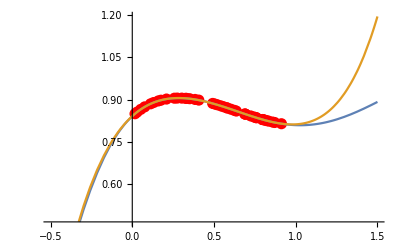

```mathematica
{m,n}={43,6};
g[x_]:= Sin[x+Cos[Sin[x]+ArcTan[x]]]
xs= RandomReal[{0,1},m];
fs[x_]:=Table[x^j,{j,0,n-1}]
A=Map[fs,xs];
b=Map[g,xs];
as=PseudoInverse[A].b;
f[x_]:=as.fs[x]
Plot[{g[x],f[x]},{x,-0.5,1.5},
Prolog->{Red, PointSize[0.02],Point[{xs,b}ᵀ]}]
```

### Trig Fitting

{54.3616,-102.372,89.6781,-71.6549,51.9702,-34.0062,19.8264,-10.1436,4.42756,-1.58349,0.422564,-0.0702834}

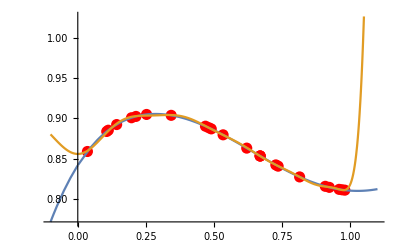

```mathematica
{m,n}={24,12};
g[x_]:= Sin[x+Cos[Sin[x]+ArcTan[x]]]
xs= RandomReal[{0,1},m];
fs[x_]:=Table[Cos[ 2 j x],{j,0,n-1}]
A=Map[fs,xs];
b=Map[g,xs];
as=PseudoInverse[A].b
f[x_]:=as.fs[x]
Plot[{g[x],f[x]},{x,-0.1,1.1},
Prolog->{Red, PointSize[0.02],Point[{xs,b}ᵀ]}]
```

### RBF Fitting

```mathematica
{m,n}={123,56};
g[{x1_,x2_}]:= Sin[x1+Cos[Sin[x2]+ArcTan[x1]]]
Omega=RegionUnion[Disk[{0,0},2],Disk[{1,1},1.6], Rectangle[{1,1.6},{3,3.6}]];
xs= RandomPoint[Omega,m];
ys=Map[g,xs];
points3D=Table[Flatten[{xs⟦i⟧,ys⟦i⟧}],{i,m}];
ϕ[r_]:=E^(-r^2)
fs[{x1_,x2_}]:=Table[ϕ[Norm[{x1,x2}-xs⟦j⟧]],{j,1,n}]
A=Map[fs,xs];
b=Map[g,xs];
as=PseudoInverse[A].b
f[x_]:=as.fs[x]
Show[
ListPointPlot3D[points3D,PlotStyle->Red],
Plot3D[{f[{x1,x2}],g[{x1,x2}]},{x1,x2}∈Omega,
PlotRange->All]
]
```

{0.437628,-1.36822,27.899,7.74831,7.59335,-5.10203,0.908675,-102.57,20.2725,1.11005,0.336223,-17.5963,50.0701,24.751,16.1631,-1.39344,-5.44618,-2.70903,-16.6074,4.13491,7.99325,-0.39146,-7.67486,67.4504,-0.232324,2.77436,0.809561,-31.5172,-1.17684,2.8285,-2.85243,-4.58239,3.04674,-30.0929,-64.9247,-98.4811,-0.0570271,-40.6117,1.09326,2.82853,-0.0948147,156.662,0.202357,33.9716,-1.61046,40.006,-6.97946,1.88562,-1.16358,-39.9192,1.03043,1.63514,-1.55168,2.92738,-1.17323,2.8642}

-Graphics3D-

```mathematica
g[{0.2,0.3}]
f[{0.2,0.3}]
```

0.882408

0.344573